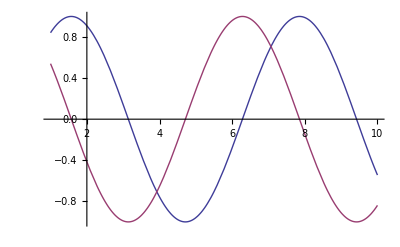

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Integrate[1/(x^4-1),x]
```

```mathematica
-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

```mathematica
1/(-1+x^4)
```

```mathematica
Simplify[e^(i*pi)]
```

e^(i pi)

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
```

```mathematica
sol=NDSolve[ode1,y,{x,-10,10}]
```

```mathematica
Plot[y[x]/.sol,{x,-10,10}]
```

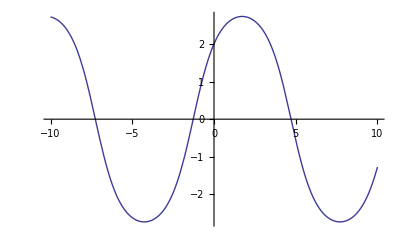
```mathematica
-Graphics-
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,50}]
```

-Graphics-

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Dynamic[Refresh[Style[(Replace[#,head_[HoldPattern[HoldPattern][symb_],rest__]:>HoldForm[head[symb,rest]]]&/@Flatten[Select[ToExpression[#,InputForm,Function[arg,Select[{OwnValues[arg],UpValues[arg],DownValues[arg]},#=!={}&],HoldAllComplete]]&/@Names["Global`*"],#=!={}&],2])//Column//StandardForm,"Input"],UpdateInterval->1]]
```

```mathematica
Do[Speak["Science rules"],{1000}]
n=2 π;
Dynamic[{Show[Graphics[{Orange,Disk[{0,0},1,{0,n}]}],Graphics[{Opacity[0],Rectangle[{-1,-1},{1,1}]}]],Speak[Round[(n*time)/(2 π)]];}]

s=0;
time=10;
sm=1;
RunScheduledTask[n=n-sm*(2 π)/time,{sm,Round[time/sm]}];
```